# b0LRW Fractal Dimension on 3d square

## Hard condition: no crossing allowed and restart when happens

### With all the points from “b0LRW - 3d - square - lattice - data - 3 - 349.csv” and “b0LRW - 3d - square - lattice - data - 351 - 1001.csv”

```mathematica
data=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b0LRWdata\\b0LRW-3d-square-lattice-data-3-349.csv"}],"CSV"],2];
```

```mathematica
data2=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b0LRWdata\\b0LRW-3d-square-lattice-data-351-1001.csv"}],"CSV"],2];
```

```mathematica
joinedData=Join[data,data2];
```

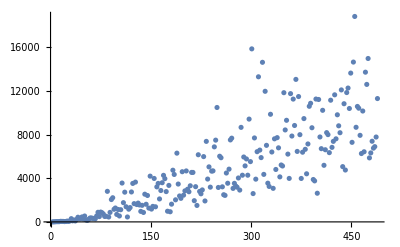

```mathematica
ListPlot[joinedData]
```

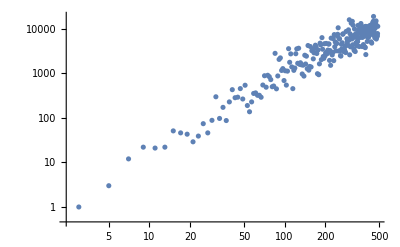

```mathematica
ListLogLogPlot[joinedData]
```

```mathematica
FindFit[Log[joinedData],a+df *x,{a,df},x]
```

{a→-0.756586,df→1.6426}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x]
```

FittedModel[…]

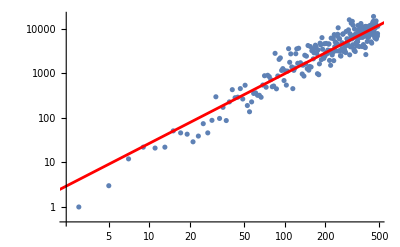

d_f=1.6426

```mathematica
Show[ListLogLogPlot[joinedData],Plot[lm[x],{x,0,1000},PlotStyle->Red]]
Print[ "d_f=",df/.FindFit[Log[joinedData],a+df *x,{a,df},x]]
```

#### Does it change if I exclude the first points?

```mathematica
nDropped=-170;
```

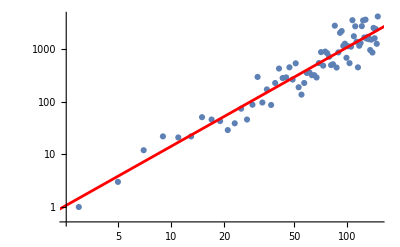

d_f=1.88557

| Estimate | Standard Error | t-Statistic | P-Value
1 | -1.68957 | 0.288347 | -5.85951 | 1.28672×10^-7
x | 1.88557 | 0.0693214 | 27.2004 | 1.30018×10^-39

```mathematica
dropped=Drop[joinedData,nDropped];
lm=LinearModelFit[Log[dropped],x,x];
Show[ListLogLogPlot[dropped],Plot[lm[x],{x,0,1000},PlotStyle->Red]]
Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x]]
lm["ParameterTable"]
```

### With all the points from “b0LRW-3d-square-lattice-data-3-501.csv”

```mathematica
data=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b0LRWdata\\b0LRW-3d-square-lattice-data-3-501.csv"}],"CSV"],2];
```

```mathematica
joinedData=Join[data];
```

```mathematica
joinedData
```

{{3,1},{5,3},{7,12},{9,6},{11,8},{13,11},{15,31},{17,42},{19,19},{21,111},{23,30},{25,80},{27,132},{29,89},{31,294},{33,115},{35,48},{37,203},{39,340},{41,287},{43,145},{45,157},{47,653},{49,281},{51,161},{53,164},{55,708},{57,201},{59,449},{61,671},{63,204},{65,254},{67,966},{69,734},{71,487},{73,1107},{75,658},{77,467},{79,855},{81,752},{83,535},{85,581},{87,852},{89,1310},{91,1869},{93,358},{95,799},{97,733},{99,1368},{101,1205},{103,2086},{105,808},{107,509},{109,1262},{111,1234},{113,1248},{115,709},{117,3341},{119,585},{121,980},{123,3656},{125,1238},{127,837},{129,2236},{131,1173},{133,3037},{135,1231},{137,3478},{139,1258},{141,2023},{143,1749},{145,1583},{147,1212},{149,1720},{151,5385},{153,1370},{155,2559},{157,1428},{159,1394},{161,6558},{163,1259},{165,8109},{167,2277},{169,1741},{171,2470},{173,1619},{175,4801},{177,2892},{179,1579},{181,3503},{183,3265},{185,4709},{187,2826},{189,1800},{191,3484},{193,7072},{195,4245},{197,1462},{199,1113},{201,4345},{203,4452},{205,2422},{207,6665},{209,4613},{211,1961},{213,3044},{215,3177},{217,4424},{219,5327},{221,2086},{223,4766},{225,2309},{227,2804},{229,3902},{231,6305},{233,4081},{235,4469},{237,4449},{239,9103},{241,4920},{243,2518},{245,3064},{247,5352},{249,3509},{251,2935},{253,5300},{255,3157},{257,7401},{259,4349},{261,4169},{263,4211},{265,5052},{267,6864},{269,5599},{271,4395},{273,6362},{275,12026},{277,3424},{279,6309},{281,3400},{283,4520},{285,4844},{287,4018},{289,4938},{291,3129},{293,4580},{295,11385},{297,7027},{299,3299},{301,11111},{303,9911},{305,4136},{307,5954},{309,6354},{311,4168},{313,2390},{315,5971},{317,5986},{319,5620},{321,4391},{323,7963},{325,9423},{327,7316},{329,6177},{331,4763},{333,10893},{335,7174},{337,3343},{339,7058},{341,5459},{343,4119},{345,12504},{347,9376},{349,6465},{351,9224},{353,2975},{355,13668},{357,10062},{359,8028},{361,9135},{363,4067},{365,7628},{367,12194},{369,5401},{371,5610},{373,19037},{375,10903},{377,9082},{379,4442},{381,5480},{383,9366},{385,20656},{387,7202},{389,13337},{391,15442},{393,12025},{395,15059},{397,10660},{399,8083},{401,11700},{403,7257},{405,12888},{407,6824},{409,3927},{411,6427},{413,10043},{415,10117},{417,5279},{419,4976},{421,9139},{423,8684},{425,8139},{427,12521},{429,5300},{431,5949},{433,8342},{435,10738},{437,6788},{439,6070},{441,9155},{443,6462},{445,9856},{447,7969},{449,15179},{451,7181},{453,6886},{455,10323},{457,7436},{459,14089},{461,9581},{463,12515},{465,15817},{467,8807},{469,8250},{471,10562},{473,10153},{475,9659},{477,9184},{479,7338},{481,6670},{483,7329},{485,8192},{487,10711},{489,12675},{lattice #Square},{lattice_size #1,walk_size},{3,1},{5,3},{7,20},{9,19},{11,9},{13,27},{15,17},{17,38},{19,56},{21,35},{23,37},{25,50},{27,134},{29,158},{31,63},{33,158},{35,74},{37,105},{39,528},{41,91},{43,240},{45,834},{47,261},{49,119},{51,218},{53,529},{55,556},{57,276},{59,310},{61,1165},{63,768},{65,966},{67,1056},{69,416},{71,236},{73,471},{75,563},{77,441},{79,2238},{81,423},{83,627},{85,1058},{87,1218},{89,735},{91,442},{93,537},{95,991},{97,1386},{99,1328},{101,1982},{103,2390},{105,1663},{107,1325},{109,993},{111,1082},{113,613},{115,2025},{117,1766},{119,2041},{121,3122},{123,861},{125,2794},{127,2344},{129,1783},{131,4974},{133,2891},{135,1227},{137,2705},{139,1062},{141,2352},{143,2013},{145,1551},{147,2281},{149,1584},{151,1525},{153,918},{155,3296},{157,2148},{159,3147},{161,4432},{163,1984},{165,10609},{167,1582},{169,4375},{171,994},{173,5020},{175,6716},{177,7387},{179,2757},{181,2594},{183,3227},{185,5607},{187,5386},{189,2461},{191,12634},{193,7069},{195,10189},{197,2128},{199,4082},{201,2998},{203,1568},{205,7568},{207,16560},{209,10163},{211,5212},{213,5331},{215,10589},{217,7337},{219,4136},{221,10378},{223,8178},{225,7032},{227,16994},{229,4028},{231,6106},{233,5192},{235,3259},{237,13331},{239,3064},{241,5752},{243,9014},{245,5590},{247,6857},{249,7168},{251,6272},{253,7291},{255,9737},{257,12565},{259,3456},{261,11852},{263,22924},{265,4487},{267,13314},{269,31176},{271,5643},{273,4254},{275,13556},{277,12446},{279,4841},{281,9940},{283,34828},{285,12885},{287,30847},{289,5297},{291,4497},{293,6110},{295,9548},{297,4586},{299,18143},{301,9240},{303,7234},{305,5581},{307,6919},{309,6510},{311,13489},{313,5568},{315,9096},{317,10035},{319,5901},{321,16089},{323,15334},{325,7118},{327,11970},{329,6544},{331,6139},{333,5865},{335,12249},{337,19251},{339,8238},{341,24754},{343,20442},{345,30807},{347,13401},{349,6489},{351,4900},{353,26084},{355,10821},{357,9350},{359,28700},{361,4779},{363,10569},{365,10657},{367,36015},{369,16270},{371,17110},{373,13879},{375,18968},{377,38313},{379,9437},{381,20493},{383,17385},{385,27737},{387,6004},{389,18144},{391,13025},{393,26502},{395,17488},{397,18996},{399,17469},{401,9734},{403,17972},{405,5141},{407,14006},{409,17098},{411,23818},{413,7910},{415,15636},{417,30293},{419,10834},{421,25453},{423,22439},{425,43034},{427,10596},{429,49318},{431,45367},{433,24684},{435,39490},{437,32544},{439,22811},{441,79261},{443,20788},{445,22905},{447,49030},{449,14880},{451,27228},{453,32293},{455,37066},{457,18841},{459,45152},{461,10996},{463,12703},{465,21346},{467,18035},{469,14101},{471,18046},{473,24233},{475,18610},{477,25216},{479,18437},{481,20481},{483,16843},{485,63090},{487,30127},{489,10236}}

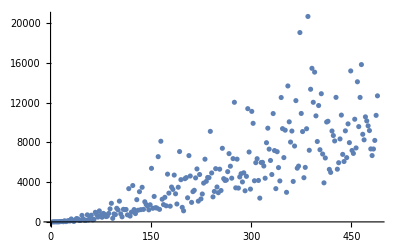

```mathematica
ListPlot[data]
```

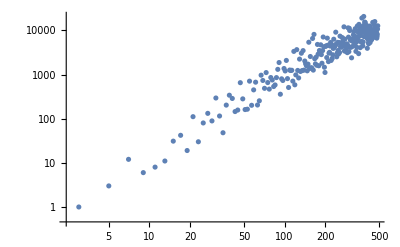

```mathematica
ListLogLogPlot[joinedData]
```

```mathematica
FindFit[Log[joinedData],a+df *x,{a,df},x]
```

{a→-1.1011,df→1.70745}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x]
```

FittedModel[…]

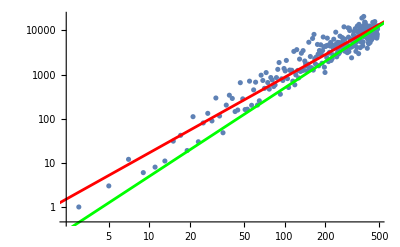

d_f=1.70745

```mathematica
Show[ListLogLogPlot[joinedData],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[joinedData],a+df *x,{a,df},x]]
```

THIS IS NOT EQUAL TO 2! IS IT BECAUSE I RESTART THE b0-LRW WHEN IT GETS TRAPPED???

### With all the points from the CLUSTER “b0LRW-3d-square-lattice-data-3-551.csv”

```mathematica
data=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b0LRWdata\\b0LRW-FromCluster\\b0LRW-3d-square-lattice-data-3-551.csv"}],"CSV"],2];
```

```mathematica
joinedData=Join[data];
```

```mathematica
joinedData
```

{{3,1},{5,3},{7,12},{9,6},{11,8},{13,11},{15,31},{17,42},{19,19},{21,111},{23,30},{25,80},{27,132},{29,89},{31,294},{33,115},{35,48},{37,203},{39,340},{41,287},{43,145},{45,157},{47,653},{49,281},{51,161},{53,164},{55,708},{57,201},{59,449},{61,671},{63,204},{65,254},{67,966},{69,734},{71,487},{73,1107},{75,658},{77,467},{79,855},{81,752},{83,535},{85,581},{87,852},{89,1310},{91,1869},{93,358},{95,799},{97,733},{99,1368},{101,1205},{103,2086},{105,808},{107,509},{109,1262},{111,1234},{113,1248},{115,709},{117,3341},{119,585},{121,980},{123,3656},{125,1238},{127,837},{129,2236},{131,1173},{133,3037},{135,1231},{137,3478},{139,1258},{141,2023},{143,1749},{145,1583},{147,1212},{149,1720},{151,5385},{153,1370},{155,2559},{157,1428},{159,1394},{161,6558},{163,1259},{165,8109},{167,2277},{169,1741},{171,2470},{173,1619},{175,4801},{177,2892},{179,1579},{181,3503},{183,3265},{185,4709},{187,2826},{189,1800},{191,3484},{193,7072},{195,4245},{197,1462},{199,1113},{201,4345},{203,4452},{205,2422},{207,6665},{209,4613},{211,1961},{213,3044},{215,3177},{217,4424},{219,5327},{221,2086},{223,4766},{225,2309},{227,2804},{229,3902},{231,6305},{233,4081},{235,4469},{237,4449},{239,9103},{241,4920},{243,2518},{245,3064},{247,5352},{249,3509},{251,2935},{253,5300},{255,3157},{257,7401},{259,4349},{261,4169},{263,4211},{265,5052},{267,6864},{269,5599},{271,4395},{273,6362},{275,12026},{277,3424},{279,6309},{281,3400},{283,4520},{285,4844},{287,4018},{289,4938},{291,3129},{293,4580},{295,11385},{297,7027},{299,3299},{301,11111},{303,9911},{305,4136},{307,5954},{309,6354},{311,4168},{313,2390},{315,5971},{317,5986},{319,5620},{321,4391},{323,7963},{325,9423},{327,7316},{329,6177},{331,4763},{333,10893},{335,7174},{337,3343},{339,7058},{341,5459},{343,4119},{345,12504},{347,9376},{349,6465},{351,9224},{353,2975},{355,13668},{357,10062},{359,8028},{361,9135},{363,4067},{365,7628},{367,12194},{369,5401},{371,5610},{373,19037},{375,10903},{377,9082},{379,4442},{381,5480},{383,9366},{385,20656},{387,7202},{389,13337},{391,15442},{393,12025},{395,15059},{397,10660},{399,8083},{401,11700},{403,7257},{405,12888},{407,6824},{409,3927},{411,6427},{413,10043},{415,10117},{417,5279},{419,4976},{421,9139},{423,8684},{425,8139},{427,12521},{429,5300},{431,5949},{433,8342},{435,10738},{437,6788},{439,6070},{441,9155},{443,6462},{445,9856},{447,7969},{449,15179},{451,7181},{453,6886},{455,10323},{457,7436},{459,14089},{461,9581},{463,12515},{465,15817},{467,8807},{469,8250},{471,10562},{473,10153},{475,9659},{477,9184},{479,7338},{481,6670},{483,7329},{485,8192},{487,10711},{489,12675},{lattice #Square},{lattice_size #1,walk_size},{3,1},{5,3},{7,20},{9,19},{11,9},{13,27},{15,17},{17,38},{19,56},{21,35},{23,37},{25,50},{27,134},{29,158},{31,63},{33,158},{35,74},{37,105},{39,528},{41,91},{43,240},{45,834},{47,261},{49,119},{51,218},{53,529},{55,556},{57,276},{59,310},{61,1165},{63,768},{65,966},{67,1056},{69,416},{71,236},{73,471},{75,563},{77,441},{79,2238},{81,423},{83,627},{85,1058},{87,1218},{89,735},{91,442},{93,537},{95,991},{97,1386},{99,1328},{101,1982},{103,2390},{105,1663},{107,1325},{109,993},{111,1082},{113,613},{115,2025},{117,1766},{119,2041},{121,3122},{123,861},{125,2794},{127,2344},{129,1783},{131,4974},{133,2891},{135,1227},{137,2705},{139,1062},{141,2352},{143,2013},{145,1551},{147,2281},{149,1584},{151,1525},{153,918},{155,3296},{157,2148},{159,3147},{161,4432},{163,1984},{165,10609},{167,1582},{169,4375},{171,994},{173,5020},{175,6716},{177,7387},{179,2757},{181,2594},{183,3227},{185,5607},{187,5386},{189,2461},{191,12634},{193,7069},{195,10189},{197,2128},{199,4082},{201,2998},{203,1568},{205,7568},{207,16560},{209,10163},{211,5212},{213,5331},{215,10589},{217,7337},{219,4136},{221,10378},{223,8178},{225,7032},{227,16994},{229,4028},{231,6106},{233,5192},{235,3259},{237,13331},{239,3064},{241,5752},{243,9014},{245,5590},{247,6857},{249,7168},{251,6272},{253,7291},{255,9737},{257,12565},{259,3456},{261,11852},{263,22924},{265,4487},{267,13314},{269,31176},{271,5643},{273,4254},{275,13556},{277,12446},{279,4841},{281,9940},{283,34828},{285,12885},{287,30847},{289,5297},{291,4497},{293,6110},{295,9548},{297,4586},{299,18143},{301,9240},{303,7234},{305,5581},{307,6919},{309,6510},{311,13489},{313,5568},{315,9096},{317,10035},{319,5901},{321,16089},{323,15334},{325,7118},{327,11970},{329,6544},{331,6139},{333,5865},{335,12249},{337,19251},{339,8238},{341,24754},{343,20442},{345,30807},{347,13401},{349,6489},{351,4900},{353,26084},{355,10821},{357,9350},{359,28700},{361,4779},{363,10569},{365,10657},{367,36015},{369,16270},{371,17110},{373,13879},{375,18968},{377,38313},{379,9437},{381,20493},{383,17385},{385,27737},{387,6004},{389,18144},{391,13025},{393,26502},{395,17488},{397,18996},{399,17469},{401,9734},{403,17972},{405,5141},{407,14006},{409,17098},{411,23818},{413,7910},{415,15636},{417,30293},{419,10834},{421,25453},{423,22439},{425,43034},{427,10596},{429,49318},{431,45367},{433,24684},{435,39490},{437,32544},{439,22811},{441,79261},{443,20788},{445,22905},{447,49030},{449,14880},{451,27228},{453,32293},{455,37066},{457,18841},{459,45152},{461,10996},{463,12703},{465,21346},{467,18035},{469,14101},{471,18046},{473,24233},{475,18610},{477,25216},{479,18437},{481,20481},{483,16843},{485,63090},{487,30127},{489,10236}}

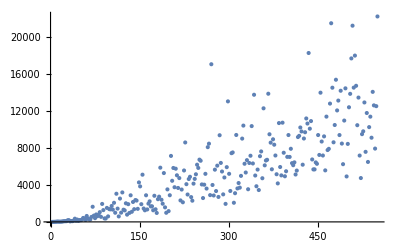

```mathematica
ListPlot[data]
```

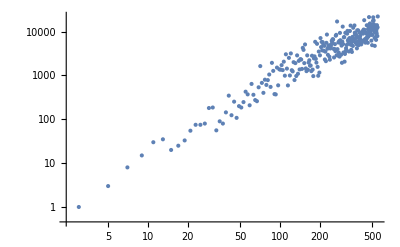

```mathematica
ListLogLogPlot[joinedData]
```

```mathematica
FindFit[Log[joinedData],a+df *x,{a,df},x]
```

{a→-0.86211,df→1.65102}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x]
```

FittedModel[…]

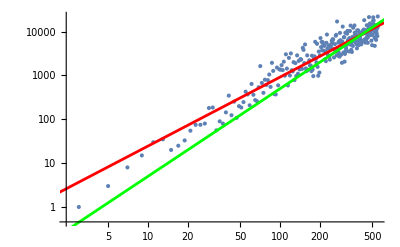

d_f=1.65102

```mathematica
Show[ListLogLogPlot[joinedData],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[joinedData],a+df *x,{a,df},x]]
```

THIS IS NOT EQUAL TO 2! IS IT BECAUSE I RESTART THE b0-LRW WHEN IT GETS TRAPPED???

#### Drop the first few

```mathematica
dropped=Drop[joinedData,10];
lm=LinearModelFit[Log[dropped],x,x]
```

FittedModel[…]

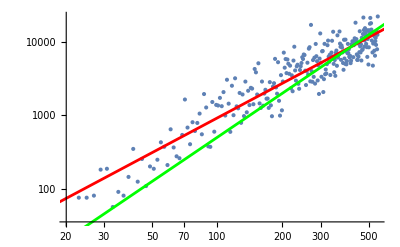

d_f=1.57315

```mathematica
Show[ListLogLogPlot[dropped],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x]]
```

## Soft crossing

### With all the points from “b0LRW-3d-square-lattice-data-3-501-softCrossing.csv”

```mathematica
data=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b0LRWdata\\b0LRW-3d-square-lattice-data-3-501-softCrossing.csv"}],"CSV"],2];
```

```mathematica
joinedData=Join[data];
```

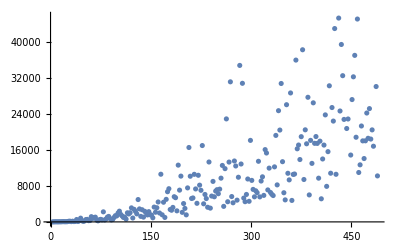

```mathematica
ListPlot[joinedData]
```

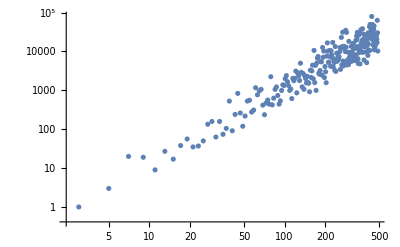

```mathematica
ListLogLogPlot[joinedData]
```

```mathematica
FindFit[Log[joinedData],a+df *x,{a,df},x]
```

{a→-1.92462,df→1.95357}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x]
```

FittedModel[…]

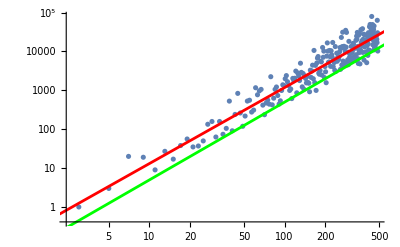

d_f=1.95357

```mathematica
Show[ListLogLogPlot[joinedData],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[joinedData],a+df *x,{a,df},x]]
```

THIS IS NOT EQUAL TO 2, BUT VERY CLOSE TO IT!!!! 
HERE WE DO NOT RESTART THE b0-LRW WHEN IT GETS TRAPPED, BUT WE LET IT CROSS ITSELF ONLY WHEN ALL THE NEIGHBORS ARE OCCUPIED

#### Drop the first few

```mathematica
dropped=Drop[joinedData,4];
lm=LinearModelFit[Log[dropped],x,x]
```

FittedModel[…]

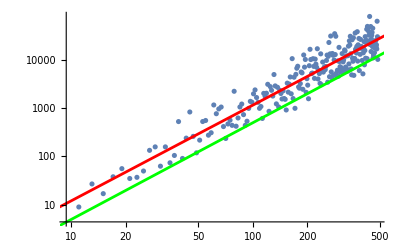

d_f=1.97898

```mathematica
Show[ListLogLogPlot[dropped],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x]]
```

It doesn’t improve much.

### With all the points from the CLUSTER “b0LRW-3d-square-lattice-data-3-709-SoftCrossing.csv”

```mathematica
data=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b0LRWdata\\b0LRW-FromCluster\\b0LRW-3d-square-lattice-data-3-709-SoftCrossing.csv"}],"CSV"],2];
```

```mathematica
joinedData=Join[data];
```

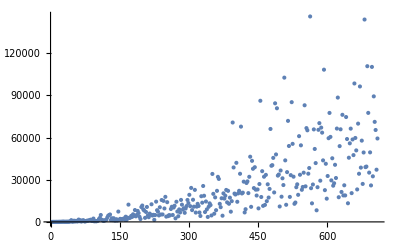

```mathematica
ListPlot[data]
```

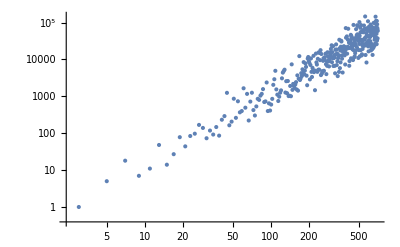

```mathematica
ListLogLogPlot[joinedData]
```

```mathematica
FindFit[Log[joinedData],a+df *x,{a,df},x]
```

{a→-1.90358,df→1.96105}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x]
```

FittedModel[…]

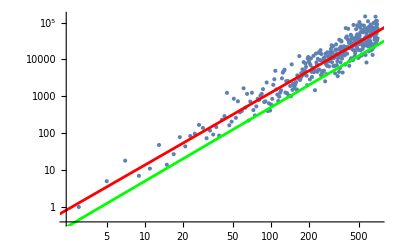

d_f=1.96105

```mathematica
Show[ListLogLogPlot[joinedData],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[joinedData],a+df *x,{a,df},x]]
```

THIS IS NOT EQUAL TO 2, BUT VERY CLOSE TO IT!!!! 
HERE WE DO NOT RESTART THE b0-LRW WHEN IT GETS TRAPPED, BUT WE LET IT CROSS ITSELF ONLY WHEN ALL THE NEIGHBORS ARE OCCUPIED

#### Drop the first few

```mathematica
dropped=Drop[joinedData,10];
lm=LinearModelFit[Log[dropped],x,x]
```

FittedModel[…]

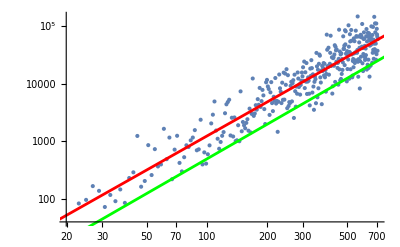

d_f=1.96417

```mathematica
Show[ListLogLogPlot[dropped],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x]]
```

It doesn’t improve it much.

### With all the points from the CLUSTER “b0LRW-3d-square-lattice-data-3-709-SoftCrossing.csv”+“b0LRW-3d-square-lattice-data-711-1001-SoftCrossing.csv”

```mathematica
data=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b0LRWdata\\b0LRW-FromCluster\\b0LRW-3d-square-lattice-data-3-709-SoftCrossing.csv"}],"CSV"],2];
```

```mathematica
data2=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b0LRWdata\\b0LRW-FromCluster\\b0LRW-3d-square-lattice-data-711-1001-SoftCrossing.csv"}],"CSV"],2];
```

```mathematica
joinedData=Join[data,data2];
```

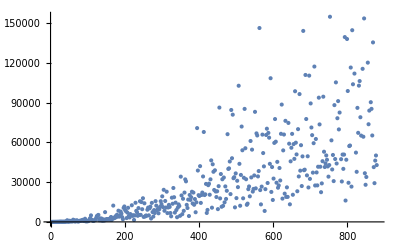

```mathematica
ListPlot[joinedData]
```

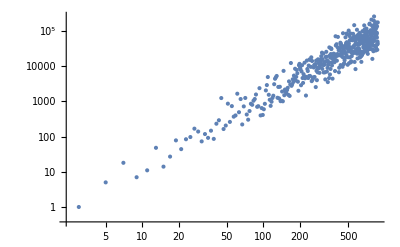

```mathematica
ListLogLogPlot[joinedData]
```

```mathematica
FindFit[Log[joinedData],a+df *x,{a,df},x]
```

{a→-1.81205,df→1.94169}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x]
```

FittedModel[…]

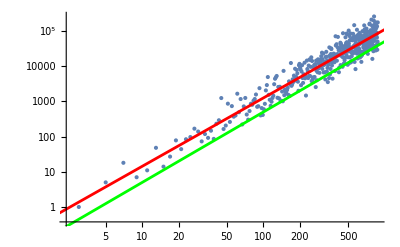

d_f=1.94169

```mathematica
Show[ListLogLogPlot[joinedData],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[joinedData],a+df *x,{a,df},x]]
```

THIS IS NOT EQUAL TO 2, BUT VERY CLOSE TO IT!!!! 
HERE WE DO NOT RESTART THE b0-LRW WHEN IT GETS TRAPPED, BUT WE LET IT CROSS ITSELF ONLY WHEN ALL THE NEIGHBORS ARE OCCUPIED

#### Drop the first few

```mathematica
dropped=Drop[joinedData,50];
lm=LinearModelFit[Log[dropped],x,x]
```

FittedModel[…]

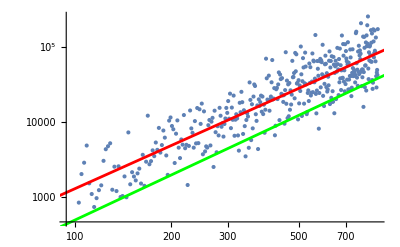

d_f=1.91581

```mathematica
Show[ListLogLogPlot[dropped],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x]]
```

It doesn’t improve it much.

## THE PREVIOUS VERSIONS ARE SPOILED BY A MISTAKE IN THE CODE: I WAS RUNNING ON 5 NEIGHBHORS INSTEAD OF 6!! HOWEVER, IT SEEMS TO POSE NO REAL PROBLEM

### With all the points from the CLUSTER “b0LRW-3d-square-lattice-data-3-881-SoftCrossing.csv”

```mathematica
data=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b0LRWdata\\b0LRW-FromCluster\\b0LRW-3d-square-lattice-data-3-881-SoftCrossing.csv"}],"CSV"],2];
```

```mathematica
data=data[[All,{1,2}]];
```

```mathematica
joinedData=Join[data];
```

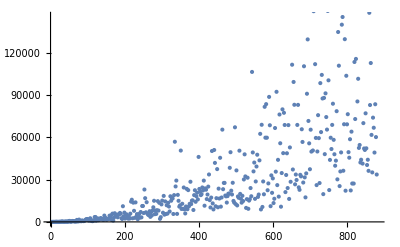

```mathematica
ListPlot[joinedData]
```

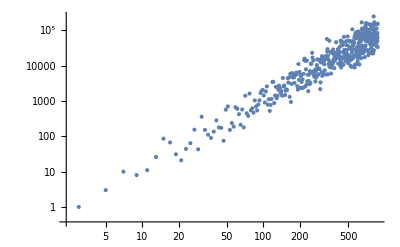

```mathematica
ListLogLogPlot[joinedData]
```

```mathematica
FindFit[Log[joinedData],a+df *x,{a,df},x]
```

{a→-2.00118,df→1.9572}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x]
```

FittedModel[…]

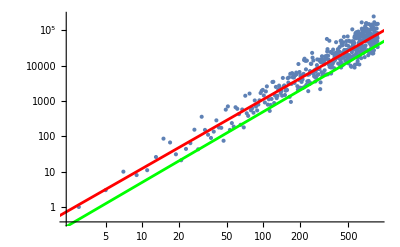

d_f=1.9572

```mathematica
Show[ListLogLogPlot[joinedData],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[joinedData],a+df *x,{a,df},x]]
```

THIS IS NOT EQUAL TO 2, BUT VERY CLOSE TO IT!!!! 
HERE WE DO NOT RESTART THE b0-LRW WHEN IT GETS TRAPPED, BUT WE LET IT CROSS ITSELF ONLY WHEN ALL THE NEIGHBORS ARE OCCUPIED

#### Drop the first few

```mathematica
dropped=Drop[joinedData,10];
lm=LinearModelFit[Log[dropped],x,x]
```

FittedModel[…]

```mathematica
Show[ListLogLogPlot[dropped],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x]]
```

-Graphics-

d_f=1.91581

It doesn’t improve it much.

### With all the points from the CLUSTER “b0LRW-3d-square-lattice-data-3-1001-SoftCrossing.csv”

```mathematica
data=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b0LRW\\b0LRWdata\\b0LRW-FromCluster\\b0LRW-3d-square-lattice-data-3-1001-SoftCrossing.csv"}],"CSV"],2];
```

```mathematica
data=data[[All,{1,2}]];
```

{{3,1},{5,3},{7,8},{9,13},{11,7},{13,32},{15,65},{17,39},{19,57},{21,33},{23,136},{25,138},{27,48},{29,197},{31,94},{33,88},{35,480},{37,212},{39,71},{41,118},{43,129},{45,231},{47,144},{49,201},{51,93},{53,422},{55,152},{57,525},{59,530},{61,222},{63,228},{65,340},{67,1168},{69,486},{71,693},{73,1520},{75,496},{77,671},{79,695},{81,520},{83,1703},{85,1004},{87,3130},{89,502},{91,1122},{93,652},{95,434},{97,2183},{99,293},{101,1130},{103,2965},{105,1160},{107,2244},{109,1034},{111,1413},{113,2239},{115,993},{117,1840},{119,1634},{121,630},{123,1715},{125,907},{127,3276},{129,2008},{131,3842},{133,1791},{135,2851},{137,3647},{139,2239},{141,1868},{143,3575},{145,4227},{147,2784},{149,2359},{151,1696},{153,1936},{155,3097},{157,2366},{159,3984},{161,3724},{163,11606},{165,2113},{167,1556},{169,4453},{171,6998},{173,4503},{175,1510},{177,2084},{179,2727},{181,1978},{183,5852},{185,2872},{187,3556},{189,3091},{191,1815},{193,9409},{195,2987},{197,3640},{199,2544},{201,4078},{203,4467},{205,2882},{207,5846},{209,4618},{211,4337},{213,3960},{215,2403},{217,4038},{219,6205},{221,1395},{223,5328},{225,5141},{227,2160},{229,9810},{231,4580},{233,4159},{235,2193},{237,5749},{239,2710},{241,3005},{243,7432},{245,7467},{247,6740},{249,3545},{251,9592},{253,8862},{255,4119},{257,19921},{259,3056},{261,10010},{263,4842},{265,10379},{267,9386},{269,7319},{271,10417},{273,14517},{275,5562},{277,14044},{279,22059},{281,17503},{283,3373},{285,14764},{287,9806},{289,9632},{291,21726},{293,2260},{295,11061},{297,6876},{299,20153},{301,39781},{303,2065},{305,14621},{307,4761},{309,23734},{311,13979},{313,4342},{315,19558},{317,6926},{319,8915},{321,4381},{323,18234},{325,6344},{327,10896},{329,9945},{331,28779},{333,14613},{335,14866},{337,20664},{339,10361},{341,25568},{343,3716},{345,28885},{347,23966},{349,9157},{351,17716},{353,7230},{355,29484},{357,40289},{359,24934},{361,5905},{363,33213},{365,7078},{367,8634},{369,25477},{371,12148},{373,23392},{375,22624},{377,41654},{379,9244},{381,39770},{383,17938},{385,14138},{387,41890},{389,7473},{391,20004},{393,7473},{395,4501},{397,8812},{399,14273},{401,9983},{403,23615},{405,10393},{407,30598},{409,9594},{411,29974},{413,62143},{415,37873},{417,9143},{419,11405},{421,10640},{423,23360},{425,18237},{427,31922},{429,15092},{431,9926},{433,20456},{435,24894},{437,21419},{439,11239},{441,35359},{443,32530},{445,18513},{447,28395},{449,17011},{451,46870},{453,41087},{455,36442},{457,10826},{459,7760},{461,36290},{463,19961},{465,32943},{467,11753},{469,23262},{471,26284},{473,33725},{475,24928},{477,60948},{479,40879},{481,45855},{483,20710},{485,11885},{487,44810},{489,19921},{491,14967},{493,23052},{495,7940},{497,31839},{499,18973},{501,13752},{503,96044},{505,70511},{507,26383},{509,16557},{511,58834},{513,26458},{515,27080},{517,28942},{519,44968},{521,16270},{523,69854},{525,22328},{527,22316},{529,23506},{531,19289},{533,31323},{535,16623},{537,67646},{539,36994},{541,29783},{543,54179},{545,56772},{547,71803},{549,75489},{551,19775},{553,23068},{555,10198},{557,20664},{559,53506},{561,15025},{563,23664},{565,52024},{567,77751},{569,36733},{571,38502},{573,52858},{575,21284},{577,102441},{579,89351},{581,19120},{583,141737},{585,111905},{587,29061},{589,31131},{591,22361},{593,23277},{595,46347},{597,15436},{599,33196},{601,33763},{603,20619},{605,23048},{607,68244},{609,39458},{611,23269},{613,170881},{615,53038},{617,51396},{619,17747},{621,51661},{623,24884},{625,61897},{627,18675},{629,55122},{631,29252},{633,51090},{635,45876},{637,86950},{639,59242},{641,16376},{643,35015},{645,89962},{647,23305},{649,55108},{651,70824},{653,104357},{655,25390},{657,22540},{659,43363},{661,91074},{663,61019},{665,84038},{667,21398},{669,31307},{671,35336},{673,42395},{675,129186},{677,27862},{679,27237},{681,57049},{683,38702},{685,40881},{687,92344},{689,43855},{691,36276},{693,109437},{695,57051},{697,98600},{699,53065},{701,28467},{703,31933},{705,34553},{707,57291},{709,87821},{711,64790},{713,51138},{715,63762},{717,74153},{719,45885},{721,50669},{723,53239},{725,41107},{727,135971},{729,44322},{731,95934},{733,34594},{735,24483},{737,32626},{739,47059},{741,136008},{743,77635},{745,39020},{747,37347},{749,66212},{751,206647},{753,82155},{755,172841},{757,60460},{759,23020},{761,105794},{763,31285},{765,25092},{767,32815},{769,34149},{771,53296},{773,36871},{775,34722},{777,70827},{779,30826},{781,206954},{783,60836},{785,251282},{787,55689},{789,83473},{791,53810},{793,106890},{795,59658},{797,36124},{799,49065},{801,92500},{803,32964},{805,123965},{807,74673},{809,63353},{811,27299},{813,310476},{815,72601},{817,88101},{819,213353},{821,39726},{823,33794},{825,95315},{827,46401},{829,118643},{831,65543},{833,138556},{835,125555},{837,57736},{839,35252},{841,163351},{843,73033},{845,47271},{847,58152},{849,85834},{851,336794},{853,42227},{855,185678},{857,42006},{859,199334},{861,136451},{863,84116},{865,167952},{867,108311},{869,126515},{871,50929},{873,57772},{875,183481},{877,39437},{879,51871},{881,40445},{883,73962},{885,115432},{887,84842},{889,29745},{891,126184},{893,98952},{895,272117},{897,74999},{899,63210},{901,40365},{903,102298},{905,259688},{907,65789},{909,85794},{911,28258},{913,121646},{915,68825},{917,115227},{919,48273},{921,439561},{923,68357},{925,124723},{927,117765},{929,43165},{931,114275},{933,180173},{935,49502},{937,81363},{939,59790},{941,30179},{943,135622},{945,61360},{947,64262},{949,153900},{951,79770},{953,72992},{955,92809},{957,101959},{959,52223},{961,40500},{963,204534},{965,136796},{967,134786},{969,37148},{971,111605},{973,185296},{975,195806},{977,81507},{979,74483},{981,117882},{983,69383},{985,91340},{987,83459},{989,84249},{991,160914},{993,107186},{995,72230},{997,78368},{999,137681},{1001,97182}}

```mathematica
joinedData=Join[data];
```

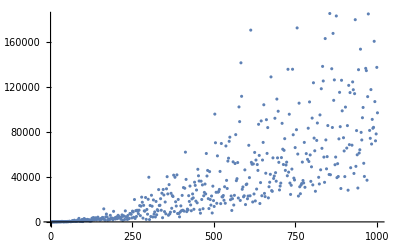

```mathematica
ListPlot[joinedData]
```

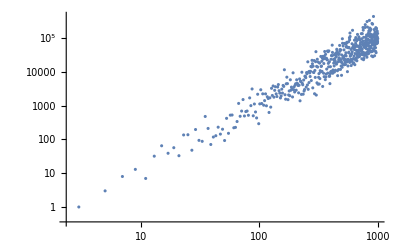

```mathematica
ListLogLogPlot[joinedData]
```

```mathematica
FindFit[Log[joinedData],a+df *x,{a,df},x]
```

{a→-2.05106,df→1.97098}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x]
```

FittedModel[…]

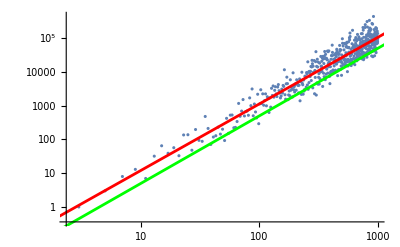

d_f=1.97098

```mathematica
Show[ListLogLogPlot[joinedData],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[joinedData],a+df *x,{a,df},x]]
```

THIS IS NOT EQUAL TO 2, BUT VERY CLOSE TO IT!!!! 
HERE WE DO NOT RESTART THE b0-LRW WHEN IT GETS TRAPPED, BUT WE LET IT CROSS ITSELF ONLY WHEN ALL THE NEIGHBORS ARE OCCUPIED

#### Drop the first few

```mathematica
dropped=Drop[joinedData,100];
lm=LinearModelFit[Log[dropped],x,x]
```

FittedModel[…]

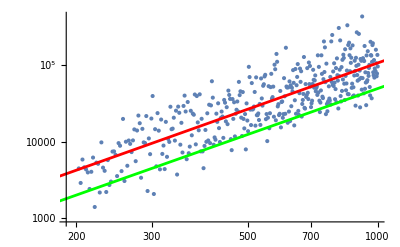

d_f=2.01301

```mathematica
Show[ListLogLogPlot[dropped],
Plot[lm[x],{x,0,1000},PlotStyle->Red],
Plot[2*x-3,{x,0,1000},PlotStyle->Green]
]
Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x]]
```

YES: IT IS EQUAL TO 2!!!!